```mathematica
e2[n_,k_]:=e2[n,k]=Sum[e2[j,k-1] e2[n/j,1],{j,Divisors[n]}];e2[n_,1]:=If[Mod[n,3]==0,-1,1];e2[1,1]:=0;e2[n_,0]:=0;e2[1,0]:=1
E2[n_,k_] := E2[n,k]=Sum[ e2[j,k],{j,2,n}]
l2[n_]:=l2[n]=Sum[(-1)^(k+1)/k e2[n,k],{k,1,Log[2,n]}]
L2[n_]:=L2[n]=Sum[(-1)^(k+1)/k E2[n,k],{k,1,Log[2,n]}]
LL2[n_]:=Sum[(-1)^(k+1)/k E2[n,k],{k,1,Log[2,n]}]
```

```mathematica
e2[12,3]
```

-3

```mathematica
Table[{n,l2[n]},{n,2,100}]//TableForm
```

2 | 1
3 | -1
4 | 1/2
5 | 1
6 | 0
7 | 1
8 | 1/3
9 | -3/2
10 | 0
11 | 1
12 | 0
13 | 1
14 | 0
15 | 0
16 | 1/4
17 | 1
18 | 0
19 | 1
20 | 0
21 | 0
22 | 0
23 | 1
24 | 0
25 | 1/2
26 | 0
27 | -7/3
28 | 0
29 | 1
30 | 0
31 | 1
32 | 1/5
33 | 0
34 | 0
35 | 0
36 | 0
37 | 1
38 | 0
39 | 0
40 | 0
41 | 1
42 | 0
43 | 1
44 | 0
45 | 0
46 | 0
47 | 1
48 | 0
49 | 1/2
50 | 0
51 | 0
52 | 0
53 | 1
54 | 0
55 | 0
56 | 0
57 | 0
58 | 0
59 | 1
60 | 0
61 | 1
62 | 0
63 | 0
64 | 1/6
65 | 0
66 | 0
67 | 1
68 | 0
69 | 0
70 | 0
71 | 1
72 | 0
73 | 1
74 | 0
75 | 0
76 | 0
77 | 0
78 | 0
79 | 1
80 | 0
81 | -15/4
82 | 0
83 | 1
84 | 0
85 | 0
86 | 0
87 | 0
88 | 0
89 | 1
90 | 0
91 | 0
92 | 0
93 | 0
94 | 0
95 | 0
96 | 0
97 | 1
98 | 0
99 | 0
100 | 0

```mathematica
L2[100]
```

268/15

```mathematica
LAdd3[n_] := Sum[ 2^k/k,{k,1,Log[3,n]}]
```

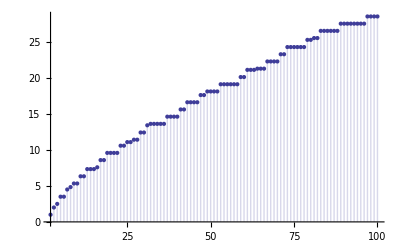

```mathematica
DiscretePlot[ LL2[n]+LAdd3[n],{n,2,100}]
```

```mathematica
P2[100,1]
```

4/5

```mathematica
E2[100,2]
```

3

```mathematica
Sum[ (-1)^( k-j), {j,2,100},{k,2,Floor[100/j]}]
```

3

```mathematica
Expand[E2[n,1]]
```

-1/2-(-1)^n/2

```mathematica
E2[x,2]
```

0

```mathematica
E2[14,2]
```

-2

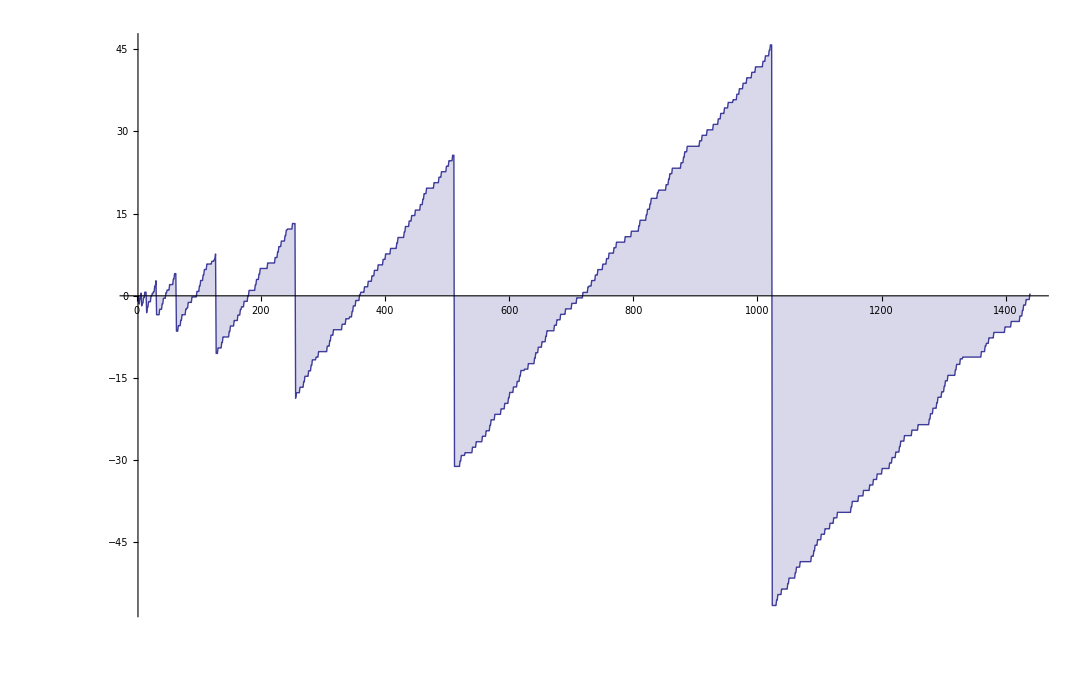

```mathematica
P2[n_,k_] := P2[n,k]=Sum[ (-1)^(j+1)( 1/k - P2[Floor[n/j],k+1]), {j,2,n}]
DiscretePlot[ P2[n,1],{n,2,90*16}]
```

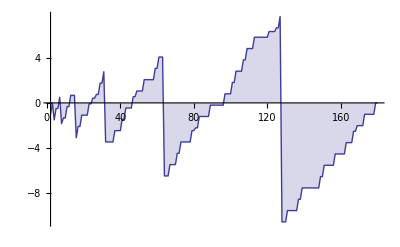

```mathematica
P2a[n_,k_] := Sum[ (-1)^(j+1)( 1/k ), {j,2,n}]+Sum[ (-1)^(j+1)( - P2a[n/j,k+1]), {j,2,n}]
DiscretePlot[ P2a[n,1],{n,2,90*2}]
```

```mathematica
Expand[Sum[ (-1)^(j+1)( 1/k ), {j,2,n}]]
```

-1/(2 k)-(-1)^n/(2 k)

```mathematica
P2a[n_, k_] :=Sum[ (-1)^(j+1), {j,2,n}]/k+Sum[ (-1)^(j+1)( - P2a[n/j,k+1]), {j,2,n}]
DiscretePlot[ P2a[n,1],{n,2,90*2}]
```

-Graphics-

```mathematica
Sum[ (-1)^(j+1), {j,2,n}]
```

1/2 (-1-(-1)^n)

```mathematica
P2a[n_, k_] :=-(1/2 (1+(-1)^n))/k+Sum[ (-1)^j( P2a[Floor[n/j],k+1]), {j,2,n}]
DiscretePlot[ P2a[n,1],{n,2,90*2}]
```

-Graphics-

```mathematica
Mod[101,3]
```

2